# t-Distributed Stochastic Neighbor Embedding

## Theme

```mathematica
fontLabels=Directive[FontFamily->"Libertinus Serif",FontSize->22];
fontTicks=Directive[FontFamily->"Libertinus Serif",FontSize->18];

(* https://mathematica.stackexchange.com/questions/54545/is-it-possible-to-define-a-new-plottheme *)
Begin["System`PlotThemeDump`"];
Themes`ThemeRules;(*preload Theme system*)

resolvePlotTheme["myThemeBasic",def:_String]:=Themes`SetWeight[
Join[
{ImageSize->Large},
{LabelStyle->fontLabels},
{TicksStyle->fontTicks},
{FrameTicksStyle->fontTicks},
(* 102 is the default grey level of Mathematica *)
{AxesStyle->Directive[AbsoluteThickness[0.3],GrayLevel[102/255]]}
]
,$ComponentWeight];
resolvePlotTheme["myTheme",def:_String]:=Themes`SetWeight[
Join[
resolvePlotTheme["myThemeBasic",def],
{PlotStyle->Directive[PointSize[0.013],Thick]}
]
,$ComponentWeight];
resolvePlotTheme["myThemeBW",def:_String]:=Themes`SetWeight[
Join[
resolvePlotTheme["myTheme",def],
{PlotStyle->Thread@Directive[{GrayLevel[0.2],GrayLevel[0.8]},Thick,{Automatic,Dashed}]}
]
,$ComponentWeight];
(* Do not adjust point sizes for region plots *)
resolvePlotTheme["myTheme",def:"RegionPlot"]:=Themes`SetWeight[
Join[
resolvePlotTheme["myThemeBasic",def],
{PlotStyle->Automatic}
]
,$ComponentWeight];

End[];

it[var_]:=Style[var,FontSlant->Italic]
bf[var_]:=Style[var,FontWeight->Bold]
bi[var_]:=bf[it[var]]
```

## Initialization

```mathematica
data={
{0.6,8},{1.66,8},{1,7.55},{1,8},
{6,9},{8,9},{6,8},{7,7},
{6,3.8},{4,2.1},{6,0.1},{8,1.95},{6,2}
};
dataLabels=Subscript[bi["x"],#]&/@Range[Length[data]];

color1=RGBColor[0.368417, 0.506779, 0.709798];
color2=RGBColor[0.880722, 0.611041, 0.142051];
```

```mathematica
SeedRandom[1337];
clusters=ClusteringComponents[data,3,1]
```

{1,1,1,1,2,2,2,2,3,3,3,3,3}

```mathematica
dataCluster=Table[
Table[x,{x,data[[Position[clusters,c]//Flatten]]}]
,{c,1,3}
]
```

{{{0.6,8},{1.66,8},{1,7.55},{1,8}},{{6,9},{8,9},{6,8},{7,7}},{{6,3.8},{4,2.1},{6,0.1},{8,1.95},{6,2}}}

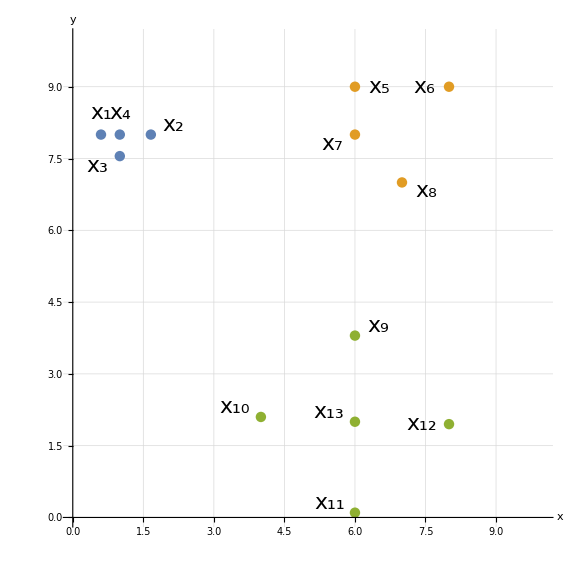

```mathematica
plotInit=Show[
ListPlot[
dataCluster,
PlotTheme->"myTheme",
GridLines->Automatic,
AspectRatio->1,
PlotRange->{{0,10.01},{0,10.01}},
AxesLabel->{x,y}
],
ListPlot[
MapThread[Callout[#1,#2]&,{data,dataLabels}],
PlotStyle->None,
PlotTheme->"myTheme"
]
]
```

## Part 1: Data Distribution

```mathematica
Subscript[p, σ_][j_,i_]:=Piecewise[{{0, i==j}, {(ⅇ^(-Norm[data[[i]]-data[[j]]]^2/(2*σ^2)))/(∑_(k=1)^Length[data] Piecewise[{{0, i==k}, {ⅇ^(-Norm[data[[i]]-data[[k]]]^2/(2*σ^2)), True}}]), True}}]
```

### Parameter σ_i

```mathematica
cf[z_]:={Opacity[0.2],ColorData["BlueGreenYellow"][z]}
```

```mathematica
Subscript[g, σ_][p1_,p2_]:=ⅇ^(-Norm[p1-p2]^2/(2*σ^2))
```

```mathematica
p3=9;
```

```mathematica
plotDist[σ_]:=Block[{plotPoints,plotProb},
plotPoints=Show[
plotInit,

ContourPlot[Subscript[g, σ][data[[p3]],{x1,x2}],{x1,0,11},{x2,0,11},
PlotTheme->"myTheme",
AspectRatio->1,
ColorFunction->(cf[#]&),
ColorFunctionScaling->False,
PlotLegends->BarLegend[{cf[#]&,{0,1}},LegendMargins->{{0,0},{0,46}}],
PerformanceGoal->"Quality",
PlotPoints->50,
PlotRange->{0,1}
],

PlotLabel->"Data points"
];
plotProb=DiscretePlot[{Subscript[p, σ][j,p3]},{j,1,Length[data]},
PlotTheme->"myTheme",
PlotRange->{0,1},
PlotLabel->"Probability distribution",
PerformanceGoal->"Quality",
AxesLabel->{it["j"],Subscript[it["p"],"j|"<>ToString[p3]]}
];

Column[{
plotPoints,
plotProb
}]
]
```

```mathematica
Manipulate[
plotDist[σ]
,{σ,0.1,5}]
```

```mathematica
(*Export[
FileNameJoin[{
NotebookDirectory[],
"frames/sigma=00.png"
}],
Table[plotDist[σ],{σ,0.1,5,0.05}],
"VideoFrames",
Antialiasing->True
];*)
```

The conditional probabilities sum indeed up to 1:

```mathematica
Table[Subscript[p, σ][j,p3],{j,1,Length[data]}]//Total//Simplify
```

1

because the denominator is the same for each p_(j|i) and when building the sum, the numerator becomes equal to the denominator. They must be positive due to the exponential function.

There must always be at least one peak since p_(j|i) is a valid probability distribution and hence must sum up to 1. The strongest peak always corresponds to the nearest data point (x_13 in this case).

For the extreme case

lim_(σ_9→0)  we get a one-hot vector (only the nearest neighbour is considered) [this question has not been asked but maybe it is nice to know :-)].

```mathematica
Table[Limit[Subscript[p, σ][j,p3],σ->0],{j,1,Length[data]}]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0,0.,0.,0.,1.}

lim_(σ_9→∞)  we get an almost uniform distribution with p_(9|9)=0 and p_(j≠9|9)=1/(n-1) (all neighbour points are considered equally).

```mathematica
Table[Limit[Subscript[p, σ][j,p3],σ->∞],{j,1,Length[data]}]
```

{0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0,0.0833333,0.0833333,0.0833333,0.0833333}

We always pick neighbours relative to some base point considering the density around the base point. But since the density around each point is different, the corresponding probabilities may be different as well. The critical factor is the scaling σ_i which is chosen per point separately.

### Perplexity

```mathematica
Subscript[H, σ_][i_]:=-∑_(j=1)^Length[data] Piecewise[{{0, Subscript[p, σ][j,i]==0}, {Subscript[p, σ][j,i]*Log2[Subscript[p, σ][j,i]], True}}]
Subscript[perp, σ_][i_]:=2^(Subscript[H, σ][i])
```

The approach here to find the σ_i values is to test a few values in a range and select the closest one.

```mathematica
perpUser=2;
sigmas=Table[
Nearest[
Table[Subscript[perp, σ][i]->σ,{σ,0.1,3,0.02}],
perpUser
],
{i,1,Length[data]}
]//Flatten
```

{0.36,0.32,0.26,0.18,0.96,0.52,0.76,0.88,0.96,0.94,1.,0.94,0.34}

```mathematica
p1=4;
p2=13;
```

```mathematica
Clear[plotPerp]
```

```mathematica
plotPerp[σMax_:3]:=Show[
ListLinePlot[{
Table[{σ,Subscript[perp, σ][p1]},{σ,0.1,σMax,0.05}],
Table[{σ,Subscript[perp, σ][p2]},{σ,0.1,σMax,0.05}]
},
PlotTheme->"myTheme",
GridLines->Automatic,
AxesLabel->{"σ_i","Perplexity"},
PlotLegends->{Subscript[bi["x"],p1],Subscript[bi["x"],p2]}
],

ListPlot[{
{Callout[{sigmas[[p1]],perpUser},"("<>ToString[sigmas[[p1]]]<>", 2)",Above,LeaderSize->20]},
{Callout[{sigmas[[p2]],perpUser},"("<>ToString[sigmas[[p2]]]<>", 2)",After,LeaderSize->14]}
},
PlotTheme->"myTheme"
]
]
```

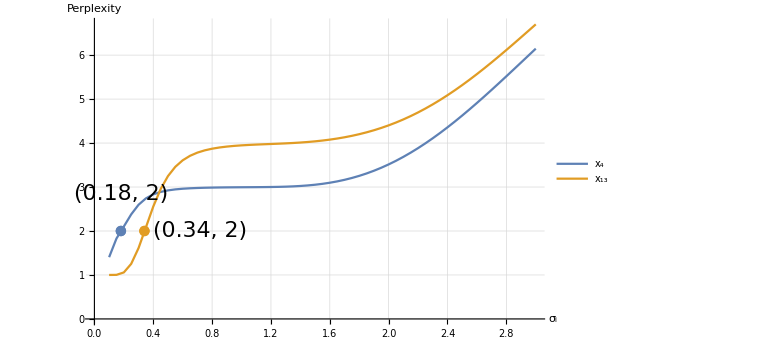

```mathematica
plotPerp[]
```

Both curves reach the plateau when the corresponding Gaussians cover all points in the near neighbourhood. The blue curve reaches the plateau first since x_4 has only 3 near neighbours in the surrounding whereby x_13 has 4 neighbours. After covering these nearby neighbours, we need to overcome some distance first before reaching the other clusters (so, the plateau comes from the space between the clusters).

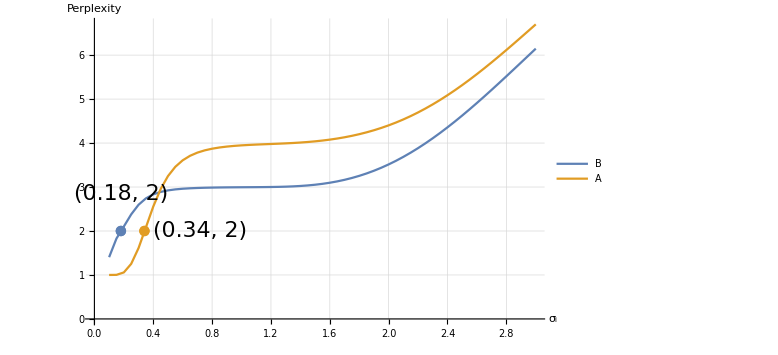

```mathematica
plotPerp[]/.{Subscript[bi["x"],p1]->"B",Subscript[bi["x"],p2]->"A"}
```

```mathematica
plotPerpProb[c1_:color1,c2_:color2]:=DiscretePlot[{Subscript[p, sigmas[[p1]]][j,p1],Subscript[p, sigmas[[p2]]][j,p2]},{j,1,Length[data]},
PlotTheme->"myTheme",
PlotRange->All,
PlotStyle->{c1,c2},
PlotLegends->PointLegend[{c1,c2},{Subscript[bi["x"],p1],Subscript[bi["x"],p2]},LegendMarkerSize->13],
AxesLabel->{it["j"],"p_(j | i)"}
]
```

```mathematica
plotPerpProb[RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.560181, 0.691569, 0.194885]]
```

-Graphics-

```mathematica
plotPerpProb[RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.560181, 0.691569, 0.194885]]/.{Subscript[bi["x"],p1]->"C",Subscript[bi["x"],p2]->"D"}
```

-Graphics-

```mathematica
TableForm[{
{Subscript[x, 4],0.18,"C",Subscript[H, sigmas[[p1]]][p1],Subscript[perp, sigmas[[p1]]][p1],"B"},
{Subscript[x, 13],0.34,"D",Subscript[H, sigmas[[p2]]][p2],Subscript[perp, sigmas[[p2]]][p2],"A"}
},TableHeadings->{None,{"Data point","Scaling","Distribution","Entropy","Perplexity","Curve"} }]
```

Data point | Scaling | Distribution | Entropy | Perplexity | Curve
x_4 | 0.18 | C | 0.993761 | 1.99137 | B
x_13 | 0.34 | D | 0.988433 | 1.98403 | A

How do the curves evolve for higher σ? The thing to know is that the perplexity is a smooth measure for the number of neighbours and since we have only 13 points, we cannot have more than 12 neighbours. Hence, both curves approach to a perplexity value of 12.

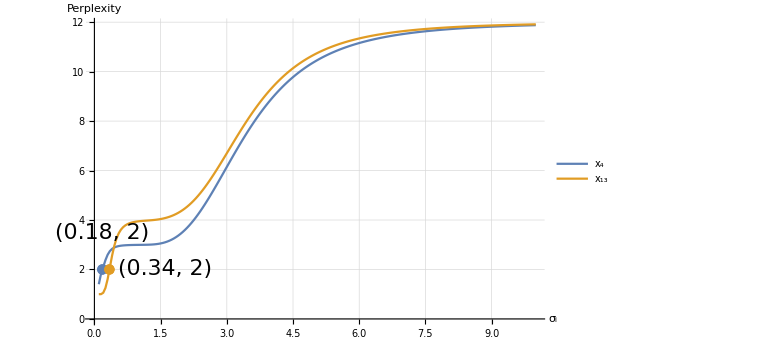

```mathematica
plotPerp[10]
```

How does the probability distribution for the two points change for the same σ value?

```mathematica
Manipulate[
DiscretePlot[{Subscript[p, σ][j,p1],Subscript[p, σ][j,p2]},{j,1,Length[data]},PlotTheme->"myTheme",PlotRange->{0,1},PerformanceGoal->"Quality"]
,{σ,0.1,1}]
```

### Symmetrize the Matrix P

```mathematica
ps[i_,j_]:=(Subscript[p, sigmas[[i]]][j,i]+Subscript[p, sigmas[[j]]][i,j])/(2*Length[data])
```

```mathematica
Table[ps[i,j],{i,1,Length[data]},{j,1,Length[data]}]//Total//Total
```

1.

```mathematica
equalNumberForm[x_,numbLeft_,numbRight_]:=Module[{digits,exponent,lengthLeft},
If[!NumberQ[x],Return[x]];
{digits,exponent}=RealDigits[x];

(* Make sure that the list is long enough *)
digits=ArrayPad[digits,{Piecewise[{{0, exponent≥0}, {Abs[exponent], True}}],numbRight}];
exponent=Max[exponent,0];
lengthLeft=Length[digits[[1;;exponent]]];

StringJoin[ToString[#]&/@ConstantArray["0",numbLeft-lengthLeft]]<>
StringJoin[ToString[#]&/@digits[[1;;lengthLeft]]]<>"."<>
StringJoin[ToString[#]&/@digits[[exponent+1;;exponent+numbRight]]]
]
```

```mathematica
(* https://mathematica.stackexchange.com/questions/16750/number-format-in-legend-labels?utm_medium=organic&utm_source=google_rich_qa&utm_campaign=google_rich_qa *)
legendNumbers[x_]:=x/.{NumberForm[y_,{w_,z_}]:>equalNumberForm[y,1,4]}
```

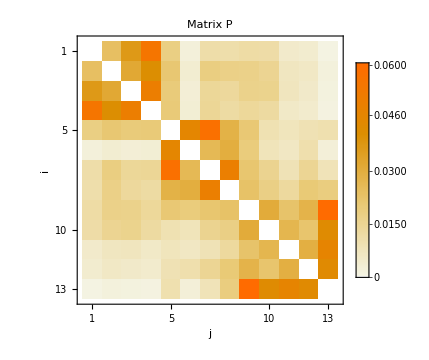

```mathematica
MatrixPlot[Table[ps[j,i],{j,1,Length[data]},{i,1,Length[data]}],
PlotTheme->"myTheme",
ImageSize->Medium,
PlotLegends->BarLegend[Automatic,LegendFunction->legendNumbers,LegendMarkerSize->310,LegendMargins->{{0,0},{0,10}}],
AspectRatio->1,
FrameLabel->{i,j},
PlotLabel->Row[{bf["Matrix "],bi["P"]}]
]
```

## Map distribution

```mathematica
SeedRandom[1337];
projInit=RandomVariate[NormalDistribution[0,0.01],Length[data]]
```

{0.0117256,-0.00417645,0.000522333,0.0000611642,0.000104979,0.00860889,-0.0103554,0.0031652,0.00220939,0.01249,0.00628762,-0.0159328,-0.00501008}

```mathematica
Subscript[y, i_][0]:=projInit[[i]];
η=0.25;
Subscript[y, i_][t_]:=Subscript[y, i][t]=Subscript[y, i][t-1]-η*4*∑_(j=1)^Length[data] (ps[i,j]-Subscript[q, t-1][i,j])(Subscript[y, i][t-1]-Subscript[y, j][t-1])(1+Norm[Subscript[y, i][t-1]-Subscript[y, j][t-1]]^2)^-1
```

```mathematica
Subscript[q, t_][i_,j_]:=1/Length[data] Piecewise[{{0, i==j}, {((1+Norm[Subscript[y, i][t]-Subscript[y, j][t]]^2)^-1)/(∑_(k=1)^Length[data] Piecewise[{{0, i==k}, {(1+Norm[Subscript[y, i][t]-Subscript[y, k][t]]^2)^-1, True}}]), True}}]
```

```mathematica
Table[Subscript[q, 0][i,j],{i,1,Length[data]},{j,1,Length[data]}]//Total//Total
```

1.

## Part 2: Optimization

### Small Example

The row for the first projection point y_1 is (0, 0, 0, 1, 0). This is not further interesting since y_1 is the point from which we want to calculate the gradient.

```mathematica
dataSmall={0,1,2,3};
```

```mathematica
pSmall={0.04,0.15,0.2};
```

q_(1j) for the other points:

```mathematica
qSmall=1/Length[dataSmall]*Table[((1+Norm[dataSmall[[1]]-dataSmall[[j]]]^2)^-1)/(∑_(k=2)^Length[dataSmall] (1+Norm[dataSmall[[1]]-dataSmall[[k]]]^2)^-1),{j,2,Length[dataSmall]}]//N
```

{0.15625,0.0625,0.03125}

The difference between the probabilities defines the force (y_2 repels, the others attract)

```mathematica
pqDiffSmall=pSmall-qSmall
```

{-0.11625,0.0875,0.16875}

In which direction to move the point?

```mathematica
yDiffSmall=Table[dataSmall[[1]]-dataSmall[[j]],{j,2,Length[dataSmall]}]
```

{-1,-2,-3}

Which scaling to use?

```mathematica
yScaleSmall=Table[(1+Norm[dataSmall[[1]]-dataSmall[[j]]]^2)^-1,{j,2,Length[dataSmall]}]
```

{1/2,1/5,1/10}

```mathematica
prodSmall=pqDiffSmall*yDiffSmall*yScaleSmall
```

{0.058125,-0.035,-0.050625}

```mathematica
TableForm[Prepend[
Table[{Row[{Subscript["y",i+1]," = 0"}],pSmall[[i]],qSmall[[i]],pqDiffSmall[[i]],yDiffSmall[[i]],yScaleSmall[[i]],prodSmall[[i]]},{i,1,3}],
{"y_1 = 0",0.0,0,0,0,1,0}
],
TableHeadings->{None,{"y_j","p_(1  j)","q_(1  j)","p_(1  j)-q_(1  j)","y_1-y_j","(1+‖y_i-y_j‖^2)^-1","Summand"}}]
```

y_j | p_(1  j) | q_(1  j) | p_(1  j)-q_(1  j) | y_1-y_j | (1+‖y_i-y_j‖^2)^-1 | Summand
y_1 = 0 | 0. | 0 | 0 | 0 | 1 | 0
y_2 = 0 | 0.04 | 0.15625 | -0.11625 | -1 | 1/2 | 0.058125
y_3 = 0 | 0.15 | 0.0625 | 0.0875 | -2 | 1/5 | -0.035
y_4 = 0 | 0.2 | 0.03125 | 0.16875 | -3 | 1/10 | -0.050625

Comparison of the exerted forces (basically, the other points from the own cluster attract and the point from the other cluster repels):

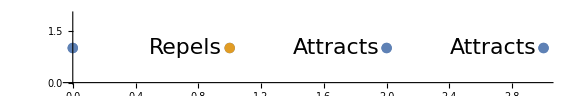

```mathematica
ListPlot[(Style[Callout[{#[[1]],1},#[[2]]],#[[3]]]&)/@Transpose[{dataSmall,{"","Repels","Attracts","Attracts"},{color1,color2,color1,color1}}],
PlotTheme->"myTheme",
Axes->{True,False},
AspectRatio->1/6,
PlotRange->{0,2}
]
```

The projection point y_1 moves to the right (where the other projection points from the same class are located)

```mathematica
-4*Total[prodSmall]
```

0.11

### Real Example

This section is mainly required for the online part.

```mathematica
cost[t_]:=cost[t]=∑_(i=1)^Length[data] ∑_(j=1)^Length[data] Piecewise[{{0, Subscript[q, t][i,j]==0}, {ps[i,j]*Log2[ps[i,j]/(Subscript[q, t][i,j])], True}}]
```

```mathematica
cost[0]
```

2.35037

```mathematica
cost[1000]
```

0.586855

```mathematica
costs=Table[cost[t],{t,0,1000}];
```

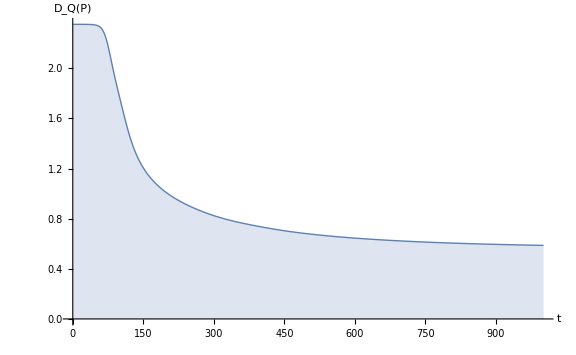

```mathematica
ListLinePlot[costs,PlotTheme->"myTheme",Filling->Axis,AxesLabel->{t,Row[{"D_Q(",it["P"],")"}]},PlotRange->All]
```

```mathematica
plotProjections[t_]:=Module[{proj,projOrdering,projCluster,pointsCluster,i},
proj=Table[Subscript[y, i][t],{i,1,Length[data]}];

(* Get a rank for each element where it appears on the line plot (https://mathematica.stackexchange.com/questions/11496/ranking-function-allowing-for-ties?utm_medium=organic&utm_source=google_rich_qa&utm_campaign=google_rich_qa) *)
projOrdering=proj/.Thread[#->Ordering@#]&@Union@proj;

(* Create list of clusters with a label per projection point *)
projCluster={};
i=1;
Do[
pointsCluster={};

Do[
AppendTo[pointsCluster,Callout[{y,0.3},Subscript[it["y"],i],Piecewise[{{Above, Mod[projOrdering[[i]],2]==0}, {Below, True}}]]];
i++;
,{y,proj[[Position[clusters,c]//Flatten]]}];

AppendTo[projCluster,pointsCluster];
,{c,1,3}];

ListPlot[projCluster,
PlotTheme->"myTheme",
AspectRatio->1/6,
Axes->{True,False},
AxesLabel->{it["y"]},
PlotRange->{Automatic,{0,0.6}},
PlotLabel->bf["Projections"],
ImagePadding->20
]
]

plotAlgo[t_]:=Module[{qProbs},
qProbs=Table[Subscript[q, t][j,i],{j,1,Length[data]},{i,1,Length[data]}];

Column[{
MatrixPlot[qProbs,
PlotTheme->"myTheme",
ImageSize->Medium,
PlotLegends->BarLegend[Automatic,LegendFunction->legendNumbers,LegendMarkerSize->310,LegendMargins->{{0,0},{0,10}}],
AspectRatio->1,
FrameLabel->{i,j},
PlotLabel->Row[{bf["Matrix "],bi["Q"]}]
],
plotProjections[t]
},Center,Spacings->1.5]
]
```

```mathematica
figures=Table[plotAlgo[t],{t,0,1000,1}];
```

```mathematica
Manipulate[
figures[[i]]
,{i,1,Length[figures],1}]
```

We have three clusters (three squares are visible in the matrix) and the first contains 4, the second also 4 and the third cluster contains 5 data points (length of the square).

```mathematica
(*Export[
FileNameJoin[{
NotebookDirectory[],
"frames/t=0000.png"
}],
figures,
"VideoFrames",
Antialiasing->True
];*)
```

## Part 3: Why Do We Use a Student’s t-Distribution?

### Crowding Problem

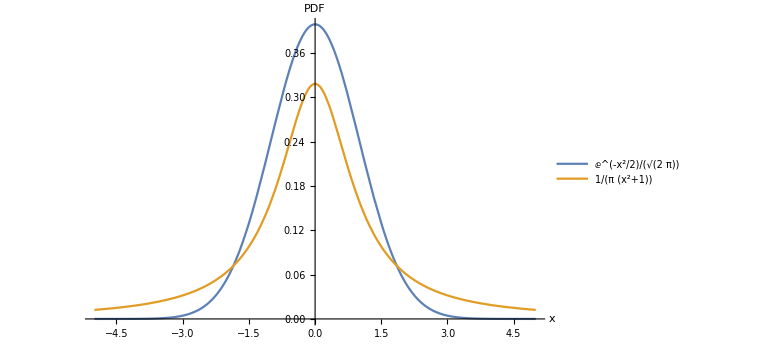

```mathematica
plotProbFunctions=Plot[{
PDF[NormalDistribution[],x],
PDF[StudentTDistribution[1],x]
},{x,-5,5},
PlotTheme->"myTheme",
PlotLegends->{PDF[NormalDistribution[],x],PDF[StudentTDistribution[1],x]},
AxesLabel->{x,"PDF"}
]
```

```mathematica
volume[r_]:={2*r,π*r^2,4/3*π*r^3}
```

In higher dimensions, we have fewer and fewer small distances (third column)

```mathematica
volume[0.5]/volume[1]
```

{0.5,0.25,0.125}

and the ratio of the larger distances increases (fourth column)

```mathematica
1-volume[0.5]/volume[1]
```

{0.5,0.75,0.875}

This is quite a huge imbalance.

### Different Distributions

```mathematica
intersection=NSolve[PDF[NormalDistribution[],x]==PDF[StudentTDistribution[1],x],x][[{1,4},1,2]]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{-1.85123,1.85123}

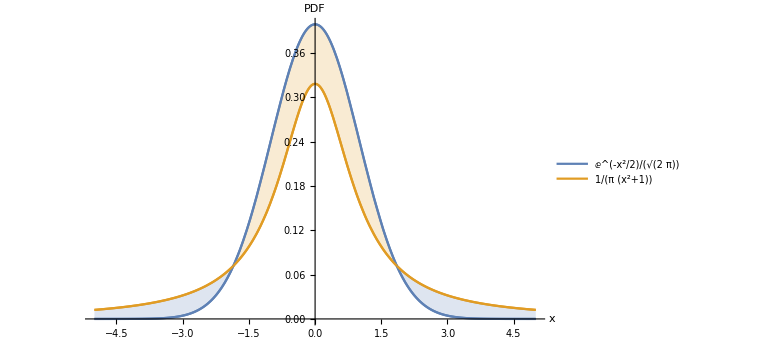

```mathematica
Show[
plotProbFunctions,
Plot[{
PDF[NormalDistribution[],x],
PDF[StudentTDistribution[1],x]
},{x,-5,intersection[[1]]},
Filling->{1->{2}}
],
Plot[{
PDF[NormalDistribution[],x],
PDF[StudentTDistribution[1],x]
},{x,intersection[[2]],5},
Filling->{1->{2}}
],
Plot[{
PDF[NormalDistribution[],x],
PDF[StudentTDistribution[1],x]
},{x,intersection[[1]],intersection[[2]]},
Filling->{2->{1}}
]
]
```

R_2 (blue region) maps distances from the feature space to larger distances in the projection space (the orange curve is above the blue curve). Since we move points in the projection space more apart, we reduce the crowding problem.

R_1 (orange region) maps distances from the feature space to smaller distances in the projection space (the orange curve is below the blue curve)

Note that this is effectively a countermeasure to the problem from earlier. We saw that we have less small and more large distances in the feature space and to simulate this relationship also in lower dimensions, we make some distances even smaller (to reduce the ratio of small distances) and some larger (to increase the ratio of large distances). In the end, we also get more misaligned distance ratios in lower dimensions. However, the choice of the t-distribution may seem a bit arbitrary. Any other distribution with similar behaviour performs probably equally good.

### t-SNE vs. SNE

```mathematica
mat=Import[FileNameJoin[{NotebookDirectory[],"comparison_result.mat"}],"LabeledData"];
circleData=FilterRules[mat,"data"][[1,2]];
projSNE=Flatten[FilterRules[mat,"projSNE"][[1,2]]];
projTSNE=Flatten[FilterRules[mat,"projTSNE"][[1,2]]];
```

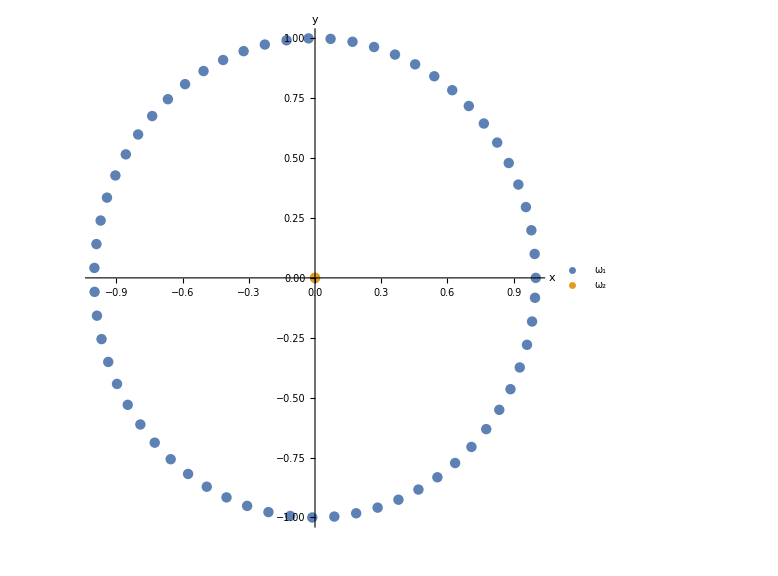

```mathematica
ListPlot[{circleData[[2;;]],{circleData[[1]]}},
PlotTheme->"myTheme",
AspectRatio->1,
AxesLabel->{x,y},
PlotLegends->PointLegend[{color1,color2},{"ω_1","ω_2"},LegendMarkerSize->13]
]
```

```mathematica
plotCircleProj[proj_,title_]:=NumberLinePlot[{proj[[2;;]],proj[[1]]},
PlotTheme->"myTheme",
PlotLabel->title,
AxesLabel->{x},
PlotLegends->PointLegend[{color2,color1},{"ω_2","ω_1"},
LegendMarkerSize->13,
LabelStyle->Directive[FontFamily->"Libertinus Serif",FontSize->22]
],
Spacings->None
]
```

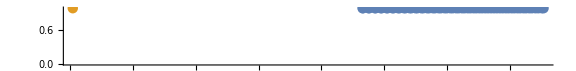
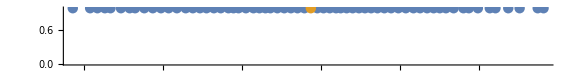

```mathematica
Column[{
plotCircleProj[projSNE,"SNE"],
plotCircleProj[projTSNE,Row[{it["t"],"-SNE"}]]
}]
```

```mathematica
Column[{
plotCircleProj[projSNE,"A"],
plotCircleProj[projTSNE,"B"]
}]
```

-Graphics-
-Graphics-

The circle is an interesting case since every blue point has the same distance to the orange point and there is no way we can model this in one dimension. However, the job of t-SNE is arguably better since it still maintains the general relationship (orange point in the middle).